```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab_iter_methods\lab_iter_methods

```mathematica
jacoby = Import["jacoby_err_vs_iter.txt", "Table"];
```

```mathematica
maxiter = jacoby[[1]][[1]]
```

60

```mathematica
jacobyInf = jacoby[[2;;maxiter+1]];
```

```mathematica
jacobyOne = jacoby[[maxiter+2;;]];
```

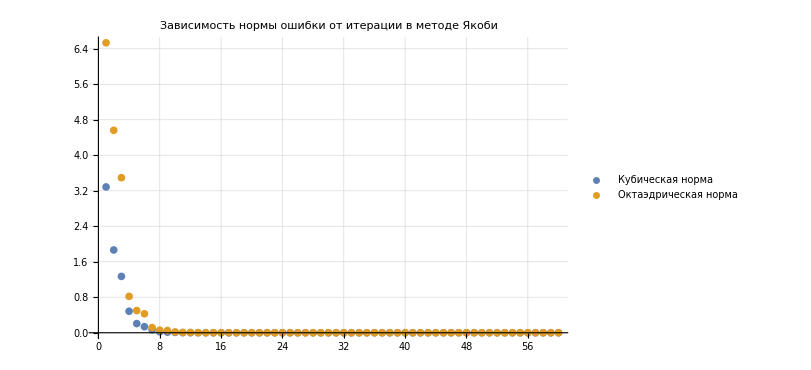

```mathematica
g1=ListPlot[{jacobyInf,jacobyOne},PlotRange->All, PlotLegends->{"Кубическая норма", "Октаэдрическая норма"},PlotLabel->"Зависимость нормы ошибки от итерации в методе Якоби",ImageSize->600,GridLines->Automatic]
```

```mathematica
relax = Import["relax_err_vs_iter.txt", "Table"];
```

```mathematica
maxiter= relax[[1]][[1]];
```

```mathematica
relaxInf = relax[[2;;maxiter+1]];
relaxOne = relax[[maxiter+2;;]];
```

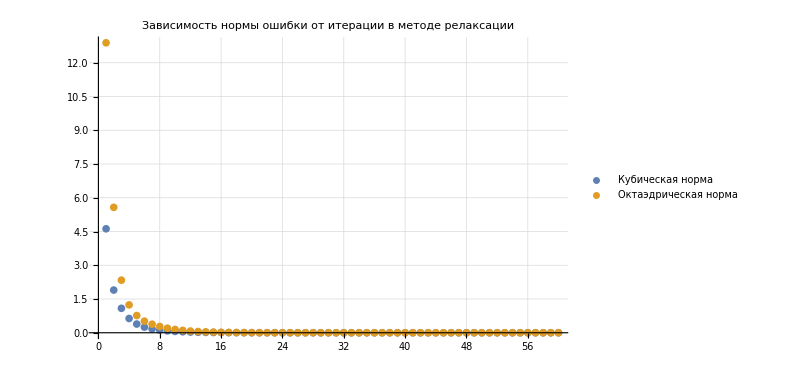

```mathematica
g2=ListPlot[{relaxInf,relaxOne},PlotRange->All, PlotLegends->{"Кубическая норма", "Октаэдрическая норма"},PlotLabel->"Зависимость нормы ошибки от итерации в методе релаксации",ImageSize->600,GridLines->Automatic]
```

```mathematica
Export["graph1_err_vs_iter_jacoby.png",g1]
```

graph1_err_vs_iter_jacoby.png

```mathematica
Export["graph1_err_vs_iter_relax.png",g2]
```

graph1_err_vs_iter_relax.png